```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/deddu/Documents/workspace/MLtests/misc

```mathematica
"/Users/deddu/Documents/workspace/MLtests/misc"
```

/Users/deddu/Documents/workspace/MLtests/misc

```mathematica
"/Users/deddu/Documents/workspace/MLtests/misc"
```

/Users/deddu/Documents/workspace/MLtests/misc

```mathematica
"."
```

.

```mathematica
en1=Reverse[Flatten[Import["english_segmentation/en_stats_10.tsv"]]];
en2=Reverse[Flatten[Import["english_segmentation/en_stats_30.tsv"]]];
en3=Reverse[Flatten[Import["english_segmentation/en_stats_60.tsv"]]];
en4=Reverse[Flatten[Import["english_segmentation/en_stats_100.tsv"]]];
en5=Reverse[Flatten[Import["english_segmentation/en_stats_200.tsv"]]];
en6=Reverse[Flatten[Import["english_segmentation/en_stats_400.tsv"]]];
```

```mathematica
fg1 = Reverse[Flatten[Import["fg_smarts_stats.tsv"]]];
```

```mathematica
d1=Reverse[Flatten[Import["smarts_stats_10.tsv"]]];
d2=Reverse[Flatten[Import["smarts_stats_30.tsv"]]];
d3=Reverse[Flatten[Import["smarts_stats_60.tsv"]]];
d4=Reverse[Flatten[Import["smarts_stats_100.tsv"]]];
d5=Reverse[Flatten[Import["smarts_stats_200.tsv"]]];
d6=Reverse[Flatten[Import["smarts_stats_400.tsv"]]];
```

```mathematica
zipfdata=Table[{i,(d/10000)⟦i⟧},{i,Length[d]}];
```

```mathematica
zipfmodel=1/(x^s ∑_(n=1)^Length[d] 1/n^s);
```

```mathematica
bettermodel=a/x+b
```

b+a/x

```mathematica
b+a/x
```

b+a/x

```mathematica
lotka=a/x^s
```

a x^-s

```mathematica
a x^-s
```

a x^-s

```mathematica
betterparams=FindFit[zipfdata⟦1;;300⟧,bettermodel,{a,s,b},x]
```

{a→0.780487 (0.503602+0.0000830723 .+0.0000151929 a-1.27486×10^-6 ac-1.35055×10^-6 ad-1.48734×10^-6 ag-1.38228×10^-6 ai-8.23569×10^-7 al-1.21502×10^-6 am+1.96307×10^-7 an-1.15759×10^-6 and-4.71558×10^-7 ar-1.49315×10^-6 are-9.36839×10^-7 as-8.64573×10^-7 at-1.48535×10^-6 ati-1.44156×10^-6 be+1.1489×10^-6 c-1.26885×10^-6 ca-1.14842×10^-6 ce-1.46383×10^-6 ch-1.26269×10^-6 ci-1.29208×10^-6 co+1.91217×10^-6 d-1.1322×10^-7 de-1.24992×10^-6 di+0.0000265061 e-1.19973×10^-6 ea-1.43889×10^-6 eb-1.13897×10^-6 ec-4.53137×10^-8 ed-1.36303×10^-6 ei-1.0871×10^-6 el-1.12923×10^-6 em-7.78704×10^-7 en-1.47498×10^-6 ent-1.48129×10^-6 eo-1.34181×10^-6 ep+1.36563×10^-6 er-1.49124×10^-6 era-3.8596×10^-7 es-9.02196×10^-7 et-1.30291×10^-6 ev-1.38949×10^-6 ew+3.98691×10^-7 f-1.46613×10^-6 fe-9.98497×10^-7 fo-1.47062×10^-6 ft-2.88348×10^-7 g-1.42191×10^-6 ge-1.37095×10^-6 gni+2.68882×10^-6 h-1.3548×10^-6 ha+7.94258×10^-7 he-1.41277×10^-6 hi-1.46839×10^-6 ho+4.74993×10^-6 i-1.37858×10^-6 ia-1.25638×10^-6 ic-1.35895×10^-6 ie-1.19176×10^-6 il-1.42776×10^-6 im+2.83721×10^-8 in-1.36703×10^-6 ing-1.31327×10^-6 io-1.40315×10^-6 ion-1.17516×10^-6 ir-9.68843×10^-7 is-6.45608×10^-7 it-1.48333×10^-6 ita+2.26351×10^-6 l-8.01652×10^-7 la-1.0757×10^-6 le-1.18358×10^-6 li-1.44419×10^-6 ll-1.32319×10^-6 lo+6.47333×10^-7 m-1.20747×10^-6 ma-1.11918×10^-6 me-1.42486×10^-6 mi-1.28647×10^-6 mo+3.87969×10^-6 n+2.92563×10^-7 na-1.48931×10^-6 nc-1.03911×10^-6 nd-7.54651×10^-7 ne-1.22236×10^-6 ng+1.08608×10^-7 ni-7.29409×10^-7 no-1.39982×10^-6 noi-1.39644×10^-6 ns-1.10883×10^-6 nt+0.0000103444 o-1.47921×10^-6 oe-9.83947×10^-7 of-1.30815×10^-6 oi-1.31829×10^-6 ol-1.28074×10^-6 om-7.0289×10^-7 on-1.40962×10^-6 op-5.81871×10^-7 or-1.06391×10^-6 ot-1.34622×10^-6 ou-1.45431×10^-6 ow-2.34217×10^-7 p-1.3373×10^-6 pe-1.40641×10^-6 po+5.93664×10^-6 r-4.30118×10^-7 ra+1.61704×10^-6 re-1.1665×10^-6 ri-5.47232×10^-7 ro-1.41892×10^-6 rs-1.23649×10^-6 rt-1.43617×10^-6 ru+7.65076×10^-6 s-9.19868×10^-7 sa-3.38808×10^-7 se-9.53152×10^-7 si-1.393×10^-6 sn-1.24329×10^-6 so-1.41587×10^-6 sr-1.02605×10^-6 st-1.33269×10^-6 su+3.2142×10^-6 t-1.3748×10^-6 T-8.44522×10^-7 ta-8.83781×10^-7 te+5.16292×10^-7 th-1.45675×10^-6 Th-6.74993×10^-7 the-6.14612×10^-7 ti-1.47711×10^-6 tion-1.09814×10^-6 tn-1.47281×10^-6 tne-1.05172×10^-6 to-1.22952×10^-6 tr-1.01252×10^-6 ts-1.44933×10^-6 tu+9.60141×10^-7 u-1.46151×10^-6 un-1.43341×10^-6 ur-1.32799×10^-6 us-1.44678×10^-6 ut-1.29756×10^-6 ve-5.10524×10^-7 w-1.43061×10^-6 wa-1.38592×10^-6 we-1.45184×10^-6 wo-1.76002×10^-7 y),s→0.,b→0.057735 (4.41243-0.0000177447 .+1.4723×10^-6 a+6.13442×10^-6 ac+6.15585×10^-6 ad+6.19458×10^-6 ag+6.16484×10^-6 ai+6.00666×10^-6 al+6.11748×10^-6 am+5.71793×10^-6 an+6.10122×10^-6 and+5.907×10^-6 ar+6.19622×10^-6 are+6.03873×10^-6 as+6.01827×10^-6 at+6.19401×10^-6 ati+6.18162×10^-6 be+5.44824×10^-6 c+6.13272×10^-6 ca+6.09863×10^-6 ce+6.18792×10^-6 ch+6.13098×10^-6 ci+6.1393×10^-6 co+5.23216×10^-6 d+5.80556×10^-6 de+6.12736×10^-6 di-1.73054×10^-6 e+6.11315×10^-6 ea+6.18086×10^-6 eb+6.09595×10^-6 ec+5.78633×10^-6 ed+6.15938×10^-6 ei+6.08127×10^-6 el+6.09319×10^-6 em+5.99396×10^-6 en+6.19108×10^-6 ent+6.19286×10^-6 eo+6.15338×10^-6 ep+5.38688×10^-6 er+6.19568×10^-6 era+5.88277×10^-6 es+6.02892×10^-6 et+6.14236×10^-6 ev+6.16688×10^-6 ew+5.66063×10^-6 f+6.18857×10^-6 fe+6.05618×10^-6 fo+6.18984×10^-6 ft+5.85514×10^-6 g+6.17605×10^-6 ge+6.16163×10^-6 gni+5.01228×10^-6 h+6.15705×10^-6 ha+5.54864×10^-6 he+6.17347×10^-6 hi+6.18921×10^-6 ho+4.42877×10^-6 i+6.16379×10^-6 ia+6.12919×10^-6 ic+6.15823×10^-6 ie+6.1109×10^-6 il+6.17771×10^-6 im+5.76547×10^-6 in+6.16052×10^-6 ing+6.1453×10^-6 io+6.17074×10^-6 ion+6.1062×10^-6 ir+6.04779×10^-6 is+5.95628×10^-6 it+6.19344×10^-6 ita+5.13269×10^-6 l+6.00046×10^-6 la+6.07804×10^-6 le+6.10858×10^-6 li+6.18236×10^-6 ll+6.14811×10^-6 lo+5.59024×10^-6 m+6.11535×10^-6 ma+6.09035×10^-6 me+6.17689×10^-6 mi+6.13771×10^-6 mo+4.67514×10^-6 n+5.69068×10^-6 na+6.19513×10^-6 nc+6.06768×10^-6 nd+5.98715×10^-6 ne+6.11956×10^-6 ng+5.74276×10^-6 ni+5.98×10^-6 no+6.1698×10^-6 noi+6.16884×10^-6 ns+6.08742×10^-6 nt+2.84495×10^-6 o+6.19228×10^-6 oe+6.05206×10^-6 of+6.14385×10^-6 oi+6.14672×10^-6 ol+6.13609×10^-6 om+5.97249×10^-6 on+6.17257×10^-6 op+5.93823×10^-6 or+6.0747×10^-6 ot+6.15463×10^-6 ou+6.18523×10^-6 ow+5.83981×10^-6 p+6.1521×10^-6 pe+6.17167×10^-6 po+4.09281×10^-6 r+5.89527×10^-6 ra+5.31571×10^-6 re+6.10375×10^-6 ri+5.92843×10^-6 ro+6.17521×10^-6 rs+6.12356×10^-6 rt+6.18009×10^-6 ru+3.60753×10^-6 s+6.03392×10^-6 sa+5.86942×10^-6 se+6.04335×10^-6 si+6.16787×10^-6 sn+6.12548×10^-6 so+6.17434×10^-6 sr+6.06398×10^-6 st+6.1508×10^-6 su+4.86354×10^-6 t+6.16272×10^-6 T+6.01259×10^-6 ta+6.02371×10^-6 te+5.62734×10^-6 th+6.18592×10^-6 Th+5.9646×10^-6 the+5.9475×10^-6 ti+6.19168×10^-6 tion+6.08439×10^-6 tn+6.19046×10^-6 tne+6.07125×10^-6 to+6.12159×10^-6 tr+6.06015×10^-6 ts+6.18382×10^-6 tu+5.50168×10^-6 u+6.18726×10^-6 un+6.17931×10^-6 ur+6.14947×10^-6 us+6.18309×10^-6 ut+6.14085×10^-6 ve+5.91804×10^-6 w+6.17852×10^-6 wa+6.16586×10^-6 we+6.18453×10^-6 wo+5.82333×10^-6 y)}

```mathematica
{a->1.6516308089676592,s->0.,b->0.18372586257636347}
```

{a→1.65163,s→0.,b→0.183726}

```mathematica
params=FindFit[zipfdata⟦1;;300⟧,zipfmodel,{s},x]
```

LinkObject::linkn: Argument LinkObject["'/Applications/Mathematica.app/SystemFiles/Links/JLink/JLink.app/Contents/MacOS/JavaApplicationStub' -init \"/tmp/m000001193471\"", 4, 4] in LinkWrite[LinkObject["'/Applications/Mathematica.app/SystemFiles/Links/JLink/JLink.app/Contents/MacOS/JavaApplicationStub' -init \"/tmp/m000001193471\"", 4, 4], CallPacket[14, {}]] has an invalid LinkObject number; the link may be closed.

LinkObject::linkn: Argument LinkObject["'/Applications/Mathematica.app/SystemFiles/Links/JLink/JLink.app/Contents/MacOS/JavaApplicationStub' -init \"/tmp/m000001193471\"", 4, 4] in LinkObject[ has an invalid LinkObject number; the link may be closed.

FindFit::nrlnum: The function value {-0.0001\ "." + zipfmodel, -0.9965 + zipfmodel, -0.0001\ "e" + zipfmodel, -0.9698 + zipfmodel, -0.0001\ "a" + zipfmodel, -0.9646 + zipfmodel, -0.0001\ "o" + zipfmodel, -0.9508 + zipfmodel, -0.0001\ "s" + zipfmodel, -0.9493 + zipfmodel, « 32 », -0.0001\ "an" + zipfmodel, -0.7573 + zipfmodel, -0.0001\ "ni" + zipfmodel, -0.733 + zipfmodel, -0.0001\ "in" + zipfmodel, -0.733 + zipfmodel, -0.0001\ "ed" + zipfmodel, -0.7112 + zipfmodel, « 250 »} is not a list of real numbers with dimensions {300} at {s} = {1.}.

FindFit[{{1,./10000},{2,1993/2000},{3,e/10000},{4,4849/5000},{5,a/10000},{6,4823/5000},{7,o/10000},{8,2377/2500},{9,s/10000},{10,9493/10000},{11,r/10000},{12,592/625},{13,i/10000},{14,4721/5000},{15,n/10000},{16,9409/10000},{17,t/10000},{18,1157/1250},{19,h/10000},{20,9041/10000},{21,l/10000},{22,4391/5000},{23,d/10000},{24,8649/10000},{25,re/10000},{26,8293/10000},{27,er/10000},{28,8293/10000},{29,c/10000},{30,8139/10000},{31,u/10000},{32,4053/5000},{33,he/10000},{34,4021/5000},{35,m/10000},{36,7973/10000},{37,th/10000},{38,7663/10000},{39,f/10000},{40,7579/10000},{41,na/10000},{42,7573/10000},{43,an/10000},{44,7573/10000},{45,ni/10000},{46,733/1000},{47,in/10000},{48,733/1000},{49,ed/10000},{50,889/1250},{51,de/10000},{52,889/1250},{53,y/10000},{54,3553/5000},{55,p/10000},{56,7077/10000},{57,g/10000},{58,3513/5000},{59,se/10000},{60,877/1250},{61,es/10000},{62,877/1250},{63,ra/10000},{64,6973/10000},{65,ar/10000},{66,6973/10000},{67,w/10000},{68,1743/2500},{69,ro/10000},{70,1743/2500},{71,or/10000},{72,1743/2500},{73,ti/10000},{74,3463/5000},{75,it/10000},{76,3463/5000},{77,the/10000},{78,6899/10000},{79,on/10000},{80,831/1250},{81,no/10000},{82,831/1250},{83,ne/10000},{84,414/625},{85,en/10000},{86,414/625},{87,la/10000},{88,823/1250},{89,al/10000},{90,823/1250},{91,ta/10000},{92,819/1250},{93,at/10000},{94,819/1250},{95,te/10000},{96,6463/10000},{97,et/10000},{98,6463/10000},{99,sa/10000},{100,6449/10000},{101,as/10000},{102,6449/10000},{103,si/10000},{104,16/25},{105,is/10000},{106,16/25},{107,of/10000},{108,6219/10000},{109,fo/10000},{110,6219/10000},{111,ts/10000},{112,1487/2500},{113,st/10000},{114,1487/2500},{115,nd/10000},{116,737/1250},{117,to/10000},{118,573/1000},{119,ot/10000},{120,573/1000},{121,le/10000},{122,5613/10000},{123,el/10000},{124,5613/10000},{125,tn/10000},{126,5513/10000},{127,nt/10000},{128,5513/10000},{129,me/10000},{130,663/1250},{131,em/10000},{132,663/1250},{133,ec/10000},{134,2613/5000},{135,ce/10000},{136,2613/5000},{137,and/10000},{138,4907/10000},{139,ri/10000},{140,4887/10000},{141,ir/10000},{142,4887/10000},{143,li/10000},{144,2437/5000},{145,il/10000},{146,2437/5000},{147,ea/10000},{148,599/1250},{149,ma/10000},{150,2347/5000},{151,am/10000},{152,2347/5000},{153,ng/10000},{154,4611/10000},{155,tr/10000},{156,4571/10000},{157,rt/10000},{158,4571/10000},{159,so/10000},{160,2257/5000},{161,di/10000},{162,2237/5000},{163,ic/10000},{164,4441/10000},{165,ci/10000},{166,4441/10000},{167,ca/10000},{168,219/500},{169,ac/10000},{170,219/500},{171,om/10000},{172,4349/10000},{173,mo/10000},{174,4349/10000},{175,co/10000},{176,271/625},{177,ve/10000},{178,861/2000},{179,ev/10000},{180,861/2000},{181,oi/10000},{182,4169/10000},{183,io/10000},{184,4169/10000},{185,ol/10000},{186,989/2500},{187,lo/10000},{188,989/2500},{189,us/10000},{190,3843/10000},{191,su/10000},{192,3843/10000},{193,pe/10000},{194,3829/10000},{195,ep/10000},{196,3829/10000},{197,ou/10000},{198,1913/5000},{199,ad/10000},{200,3809/10000},{201,ha/10000},{202,3797/10000},{203,ie/10000},{204,949/2500},{205,ei/10000},{206,949/2500},{207,ing/10000},{208,3793/10000},{209,gni/10000},{210,3793/10000},{211,T/10000},{212,3689/10000},{213,ia/10000},{214,1837/5000},{215,ai/10000},{216,1837/5000},{217,we/10000},{218,3603/10000},{219,ew/10000},{220,3603/10000},{221,sn/10000},{222,177/500},{223,ns/10000},{224,177/500},{225,noi/10000},{226,703/2000},{227,ion/10000},{228,703/2000},{229,po/10000},{230,3471/10000},{231,op/10000},{232,3471/10000},{233,hi/10000},{234,3467/10000},{235,sr/10000},{236,3419/10000},{237,rs/10000},{238,3419/10000},{239,ge/10000},{240,827/2500},{241,mi/10000},{242,3217/10000},{243,im/10000},{244,3217/10000},{245,wa/10000},{246,3201/10000},{247,ur/10000},{248,196/625},{249,ru/10000},{250,196/625},{251,eb/10000},{252,309/1000},{253,be/10000},{254,309/1000},{255,ll/10000},{256,383/1250},{257,ut/10000},{258,1531/5000},{259,tu/10000},{260,1531/5000},{261,wo/10000},{262,1523/5000},{263,ow/10000},{264,1523/5000},{265,Th/10000},{266,303/1000},{267,1/10000},{268,3013/10000},{269,un/10000},{270,2993/10000},{271,ch/10000},{272,2971/10000},{273,fe/10000},{274,371/1250},{275,ho/10000},{276,2967/10000},{277,ft/10000},{278,1481/5000},{279,tne/10000},{280,737/2500},{281,ent/10000},{282,737/2500},{283,tion/10000},{284,2907/10000},{285,oe/10000},{286,1441/5000},{287,eo/10000},{288,1441/5000},{289,ita/10000},{290,1403/5000},{291,ati/10000},{292,1403/5000},{293,ag/10000},{294,2773/10000},{295,nc/10000},{296,1383/5000},{297,era/10000},{298,1359/5000},{299,are/10000},{300,1359/5000}},zipfmodel,{s},x]

```mathematica
{s->1.547397078929903}
```

{s→1.5474}

```mathematica
{s->1.5303992415579273}
```

{s→1.5304}

```mathematica
lotkaparams=FindFit[lotka,lotka,{a,s,b},x]
```

FindFit::fitd: First argument a\ x^-s in FindFit is not a list or a rectangular array.

FindFit[a x^-s,a x^-s,{a,s,b},x]

```mathematica
p1=LogLogPlot[model/.params,{x,1,Length[zipfdata]},PlotStyle->{Thick,Red},PlotRange->{0,1}]
```

LinkObject::linkn: Argument LinkObject["'/Applications/Mathematica.app/SystemFiles/Links/JLink/JLink.app/Contents/MacOS/JavaApplicationStub' -init \"/tmp/m000001193471\"", 4, 4] in LinkWrite[LinkObject["'/Applications/Mathematica.app/SystemFiles/Links/JLink/JLink.app/Contents/MacOS/JavaApplicationStub' -init \"/tmp/m000001193471\"", 4, 4], CallPacket[14, {}]] has an invalid LinkObject number; the link may be closed.

LinkObject::linkn: Argument LinkObject["'/Applications/Mathematica.app/SystemFiles/Links/JLink/JLink.app/Contents/MacOS/JavaApplicationStub' -init \"/tmp/m000001193471\"", 4, 4] in LinkObject[ has an invalid LinkObject number; the link may be closed.

General::ivar: 0.000202174 is not a valid variable.

ReplaceAll::reps: {FindFit[{{1, "."/10000}, {2, 1993/2000}, {3, "e"/10000}, {4, 4849/5000}, {5, "a"/10000}, {6, 4823/5000}, {7, "o"/10000}, {8, 2377/2500}, {9, "s"/10000}, {10, 9493/10000}, {11, "r"/10000}, {12, 592/625}, {13, "i"/10000}, {14, 4721/5000}, « 24 », {39, "f"/10000}, {40, 7579/10000}, {41, "na"/10000}, {42, 7573/10000}, {43, "an"/10000}, {44, 7573/10000}, {45, "ni"/10000}, {46, 733/1000}, {47, "in"/10000}, {48, 733/1000}, {49, "ed"/10000}, {50, 889/1250}, « 250 »}, zipfmodel, {s}, « 22 »]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::ivar: 0.000202174 is not a valid variable.

LinkObject::linkn: Argument LinkObject["'/Applications/Mathematica.app/SystemFiles/Links/JLink/JLink.app/Contents/MacOS/JavaApplicationStub' -init \"/tmp/m000001193471\"", 4, 4] in LinkWrite[LinkObject["'/Applications/Mathematica.app/SystemFiles/Links/JLink/JLink.app/Contents/MacOS/JavaApplicationStub' -init \"/tmp/m000001193471\"", 4, 4], CallPacket[14, {}]] has an invalid LinkObject number; the link may be closed.

General::stop: Further output of General :: ivar will be suppressed during this calculation.

ReplaceAll::reps: {FindFit[{{1., 0.0001\ "."}, {2., 0.9965}, {3., 0.0001\ "e"}, {4., 0.9698}, {5., 0.0001\ "a"}, {6., 0.9646}, {7., 0.0001\ "o"}, {8., 0.9508}, {9., 0.0001\ "s"}, {10., 0.9493}, {11., 0.0001\ "r"}, {12., 0.9472}, « 28 », {41., 0.0001\ "na"}, {42., 0.7573}, {43., 0.0001\ "an"}, {44., 0.7573}, {45., 0.0001\ "ni"}, {46., 0.733}, {47., 0.0001\ "in"}, {48., 0.733}, {49., 0.0001\ "ed"}, {50., 0.7112}, « 250 »}, « 9 », « 1 », « 22 »]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {FindFit[« 1 »]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

-Graphics-

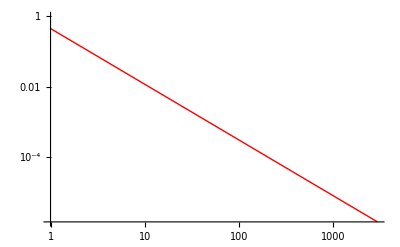

-Graphics-

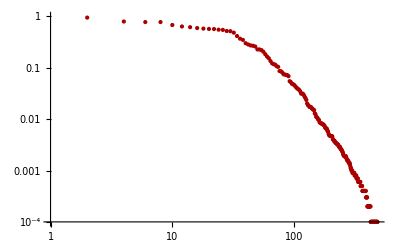

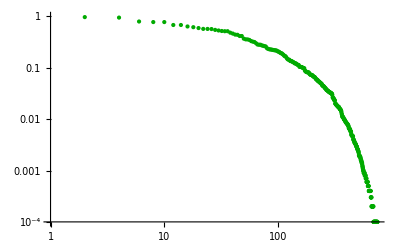

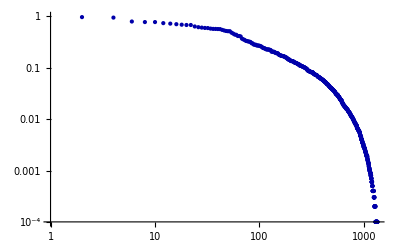

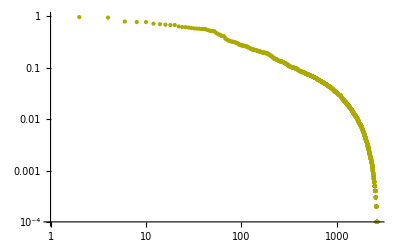

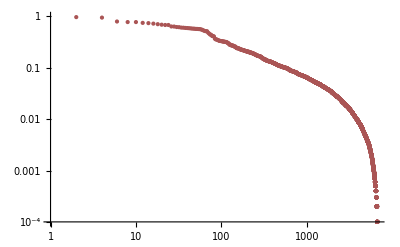

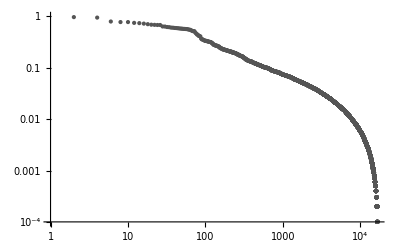

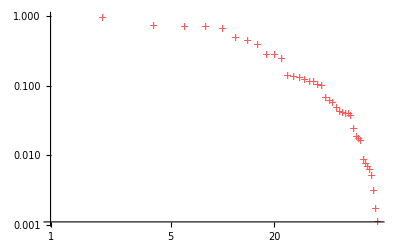

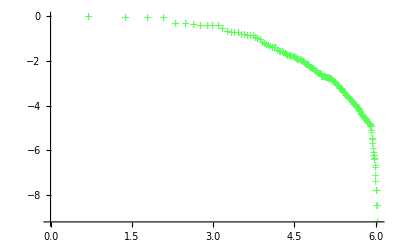

```mathematica
pp1=ListLogLogPlot[d1/10000,PlotRange->{{1,Length[d1]},{0,1}},PlotStyle->{Thick,Darker[Red]}]
pp2=ListLogLogPlot[d2/10000,PlotRange->{{1,Length[d2]},{0,1}},PlotStyle->{Thick,Darker[Green]}]
pp3=ListLogLogPlot[d3/10000,PlotRange->{{1,Length[d3]},{0,1}},PlotStyle->{Thick,Darker[Blue]}]
pp4=ListLogLogPlot[d4/10000,PlotRange->{{1,Length[d4]},{0,1}},PlotStyle->{Thick,Darker[Yellow]}]
pp5=ListLogLogPlot[d5/10000,PlotRange->{{1,Length[d5]},{0,1}},PlotStyle->{Thick,Darker[Pink]}]
pp6=ListLogLogPlot[d6/10000,PlotRange->{{1,Length[d6]},{0,1}},PlotStyle->{Thick,Darker[Gray]}]
pe1=ListLogLogPlot[en1/10000,PlotRange->{{1,Length[en1]},{0,1}},PlotStyle->{Thick,Lighter[Red]},PlotMarkers->{"+"}]
pe2=ListLogLogPlot[en2/10000,PlotRange->{{1,Length[en2]},{0,1}},PlotStyle->{Thick,Lighter[Green]},PlotMarkers->{"+"}]
pe3=ListLogLogPlot[en3/10000,PlotRange->{{1,Length[en3]},{0,1}},PlotStyle->{Thick,Lighter[Blue]},PlotMarkers->{"+"}]
pe4=ListLogLogPlot[en4/10000,PlotRange->{{1,Length[en4]},{0,1}},PlotStyle->{Thick,Lighter[Yellow]},PlotMarkers->{"+"}]
pe5=ListLogLogPlot[en5/10000,PlotRange->{{1,Length[en5]},{0,1}},PlotStyle->{Thick,Lighter[Pink]},PlotMarkers->{"+"}]
pe6=ListLogLogPlot[en6/10000,PlotRange->{{1,Length[en6]},{0,1}},PlotStyle->{Thick,Lighter[Gray]},PlotMarkers->{"+"}]
```

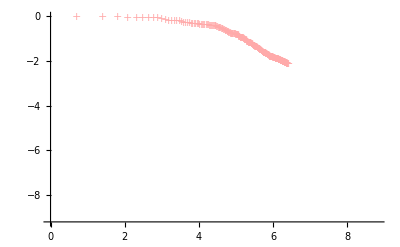

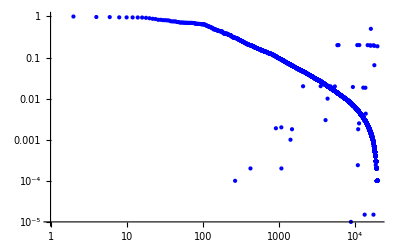

```mathematica
p2=ListLogLogPlot[d/10000,PlotRange->{{1,Length[d]},{0,1}},PlotStyle->{Thick,Blue}]
```

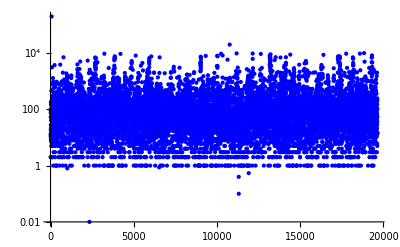

-Graphics-

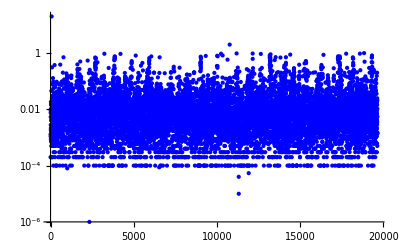

-Graphics-

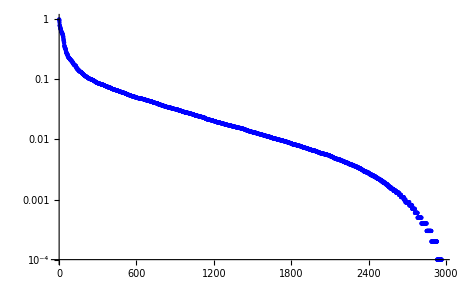

-Graphics-

```mathematica
Needs["PlotLegends`"]
```

```mathematica
Export["ChemistryAsALanguage.png",Show[pp6,pe6,pp5,pe5,pp4,pe4,pp3,pe3, pp2, pe2, pp1,pe1,FrameLabel->{"Rank","Frequency"},ImageSize->800,RotateLabel->True] ]
```

ChemistryAsALanguage.png

```mathematica
Export["English.pdf",p4]
```

English.pdf

```mathematica
Export["Chemistry.pdf",p2]
```

Chemistry.pdf

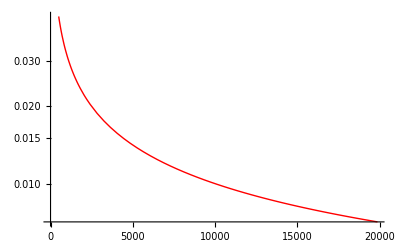

```mathematica
p3=LogPlot[1/x^{1/2},{x,1,Length[zipfdata]},PlotStyle->{Thick,Red}]
```

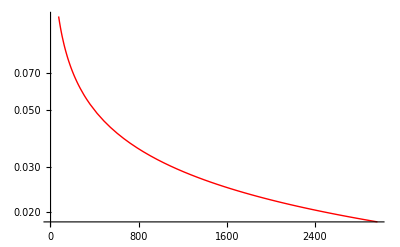

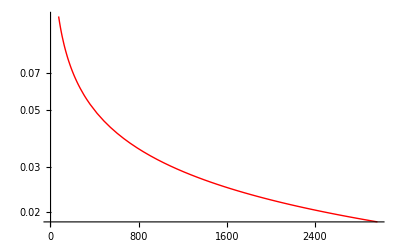

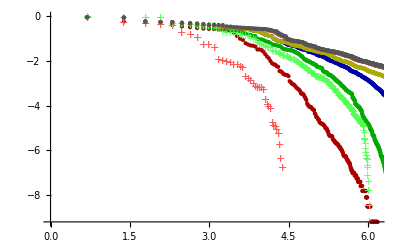

```mathematica
Show[pp1,pe1,pp2,pe2,pp3,pe3, pp4, pe4, pp5,pe5,pp6,pe6]
```

```mathematica
data=Import["/tmp/wars.csv"]⟦1;;All,2;;3⟧
```

{{D,4},{R,12},{R,3},{R,7},{R,5},{R,0},{R,1},{D,2},{R,4},{D,1},{R,11},{R,0},{R,1},{D,12},{R,0},{R,0},{R,0},{D,32},{D,5},{R,1},{D,0},{D,2},{R,0},{R,0},{D,0},{R,7},{R,5},{D,4},{R,9},{D,2}}

```mathematica
??If
```

If[condition,t,f] gives t if condition evaluates to True, and f if it evaluates to False. 
If[condition,t,f,u] gives u if condition evaluates to neither True nor False.

Attributes[If]={HoldRest,Protected}

```mathematica
Mean[(If[#1≠0,0,1]&)/@Select[data,#1⟦1⟧=="D"&]⟦1;;All,2⟧]//N
```

0.181818

```mathematica
Mean[(If[#1≠0,0,1]&)/@Select[data,#1⟦1⟧=="R"&]⟦1;;All,2⟧]//N
```

0.368421

```mathematica
(If[#1⟦1⟧=="D",{1,#1⟦2⟧},{0,#1⟦2⟧}]&)/@data
```

{{1,4},{0,12},{0,3},{0,7},{0,5},{0,0},{0,1},{1,2},{0,4},{1,1},{0,11},{0,0},{0,1},{1,12},{0,0},{0,0},{0,0},{1,32},{1,5},{0,1},{1,0},{1,2},{0,0},{0,0},{1,0},{0,7},{0,5},{1,4},{0,9},{1,2}}

```mathematica
Export["/tmp/peace.pdf",BarChart[{0.18181818181818182,0.3684210526315789}]]
```

/tmp/peace.pdf

```mathematica
Correlation[((If[#1⟦1⟧=="D",{0,#1⟦2⟧},{1,#1⟦2⟧}]&)/@data)⟦1;;All,1⟧,((If[#1⟦1⟧=="D",{0,#1⟦2⟧},{1,#1⟦2⟧}]&)/@data)⟦1;;All,2⟧]//N
```

-0.178886

```mathematica
??Correlation
```

Correlation[v_1,v_2] gives the correlation between the vectors v_1 and v_2.
Correlation[m] gives the correlation matrix for the matrix m.
Correlation[m_1,m_2] gives the correlation matrix for the matrices m_1 and m_2.
Correlation[dist] gives the correlation matrix for the multivariate symbolic distribution dist.
Correlation[dist,i,j] gives the (i,j)^th correlation for the multivariate symbolic distribution dist.

Attributes[Correlation]={Protected,ReadProtected}
 
Options[Correlation]={}

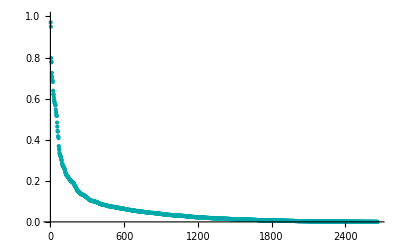

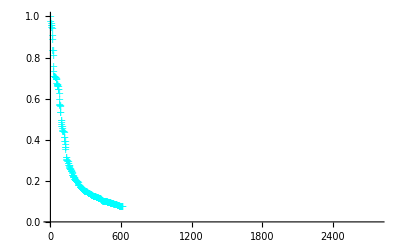

```mathematica
a=ListPlot[d4/10000,PlotRange->{{1,Length[d4]},{0,1}},PlotStyle->{Thick,Darker[Cyan]}]
b=ListPlot[en4/10000,PlotRange->{{1,Length[en4]},{0,1}},PlotStyle->{Thick,Cyan},PlotMarkers->{"+"}]
```

```mathematica
Show[a,b]
```

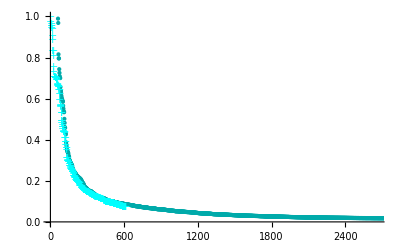

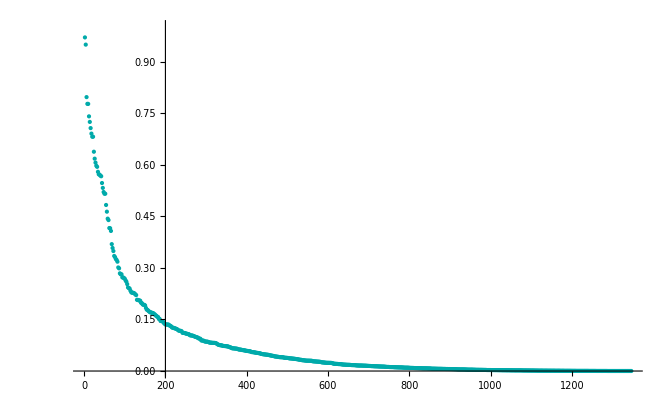

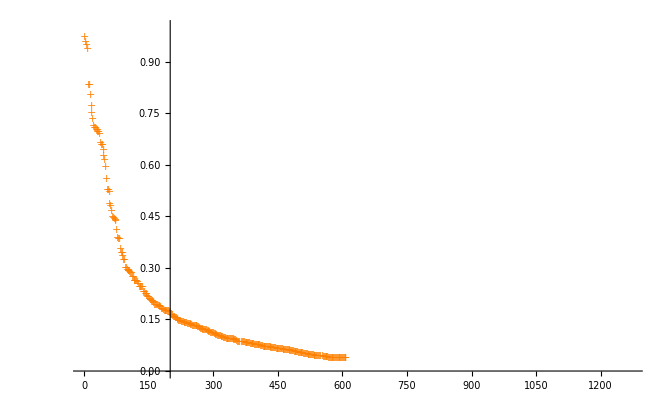

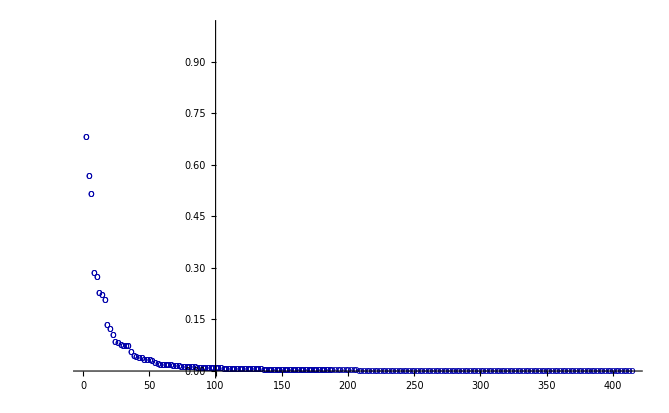

```mathematica
a=ListPlot[d3/10000,PlotRange->{{1,Length[d3]},{0,1}},PlotStyle->{Thick,Darker[Cyan]}]
b=ListPlot[en3/10000,PlotRange->{{1,Length[en3]},{0,1}},PlotStyle->{Thick,Orange},PlotMarkers->{"+"}]
c=ListPlot[fg1/10000,PlotRange->{{1,Length[fg1]},{0,1}},PlotStyle->{Thick,Darker[Blue]},PlotMarkers->{"o"}]
```

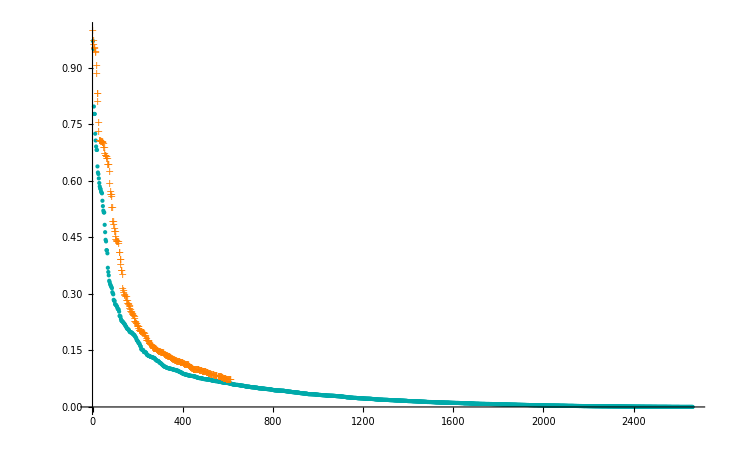

```mathematica
Show[a,b, c]
```

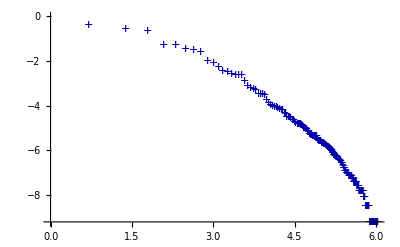

```mathematica
pfg=ListLogLogPlot[fg1/10000,PlotRange->{{1,Length[fg1]},{0,1}},PlotStyle->{Thick,Darker[Blue]},PlotMarkers->{"+"}]
```

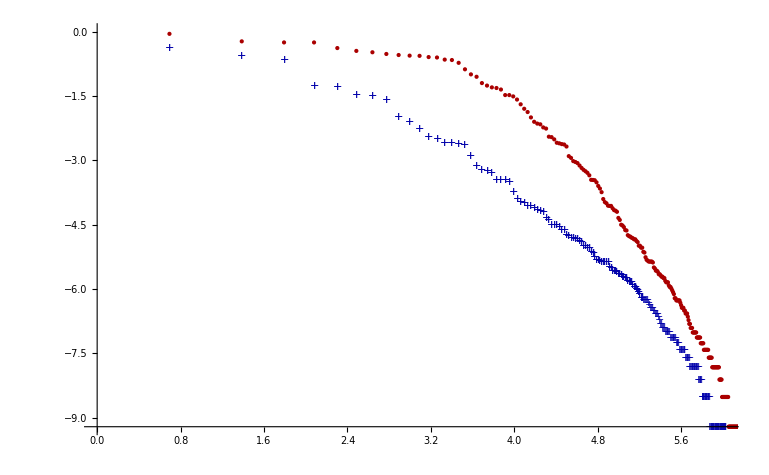

```mathematica
Show[pfg,pp1, pe1]
```